-Graphics-

# The Multiparadigm Data Science Workflow

## Sample project: Twitter data analysis

## Learning Objectives

Build a workflow to analyse data from Wolfram Research’s Twitter account to provide useful insights.

Identify Wolfram Language functionality useful at each of the stages:

Question

Wrangle

Explore

Analyse

Communicate

Reuse the workflow:

To repeat the analysis for different keywords for same account

To repeat the analysis for a different account

To build on the analysis to include new information

## From Data-Driven Questions to Actionable Insight

### Data

https://twitter.com/WolframResearch

### Questions

How many tweets were sent out and when?

What are they tweeting about?

Who is being mentioned in their tweets?

How many tweets were about “#DataScience”?

### Insight

123456

## The Project Workflow

## Question

### What Can Be Learned from the Data?

How often do they tweet?

How many tweets are liked or retweeted? Which was the most popular tweet?

What topics or hashtags do they use most often?

What is being said in the tweets?

Who is being mentioned in their tweets?

### Who Wants to Know the Results?

Who will be the audience of your analysis?

What sort of information will the audience be interested in?

Will this be a one-time analysis or will you be repeating it at regular intervals?

Can the workflow be made flexible to accommodate new data and questions?

## Wrangle

Connect to Twitter API:

```mathematica
twitter=ServiceConnect["Twitter"]
```

Download tweets made by Wolfram Research:

```mathematica
(*wolframTweets = twitter["TweetList","Username"-> "WolframResearch",MaxItems-> 5000,"Elements"-> "FullData"];*)
Get["WolframTweetsData.mx"]
```

Take a peek at the downloaded data:

```mathematica
RandomSample[wolframTweets,5]
```

```mathematica
%[5]
```

Look at the underlying structure of the data:

```mathematica
Normal[%]
```

It is possible to parse out the user mentions from the text of the tweet. Here is an example with the user mention “@wolframu”:

```mathematica
txt = "Introduction to Multiparadigm Data Science - a new course by  @wolframu - talks about a different approach to traditional #DataScience";
```

String pattern matching can be used to identify the user mention:

```mathematica
StringCases[txt,"@"~~u:(LetterCharacter|DigitCharacter|"_")..~~(WhitespaceCharacter|PunctuationCharacter|EndOfString):> u]
```

This function finds the user mention from the tweet text and adds it back as a key-value pair to the original association:

```mathematica
getUserMentions[tweet_Association]:= Module[{modifiedTweet = tweet},
AssociateTo[modifiedTweet,"user_mentions"->Flatten[StringCases[tweet["Text"],"@"~~u:(LetterCharacter|DigitCharacter|"_")..~~(WhitespaceCharacter|PunctuationCharacter|EndOfString):> u]]]
]
```

Here is an example of the association containing the data of a tweet:

```mathematica
tweetAssociation=<|"ID"->"1234","Text"->"This tweet talks about @wolframu","ThumbnailsURL"->"","Date"->DateObject[{2018,9,19},"Day","Gregorian",-5.],"Hashtags"->"Test","Location"->"","Username"->"someuser","Name"->"Some User","ProfileImageThumbnail"->"","RetweetCount"->40,"FavoriteCount"->2,"URL"->""|>;
```

Here is the result of using the getUserMentions function on the example:

```mathematica
getUserMentions[tweetAssociation]
```

Applying the getUserMentions function on the entire tweets dataset:

```mathematica
wolframTweets = Dataset[getUserMentions /@ Normal@wolframTweets]
```

Sometimes the text of the tweets needs some cleaning. Here is another example of a tweet:

```mathematica
example = "#ComputationalIntelligence &gt; #AI. Catch up on @stephen_wolfram's talk on the theory &amp; application of computational intelligence at @CollisionHQ 2018!https://t.co/nEWUTZbTxR";
```

String pattern matching can be used again to identify and delete undesirable elements from the tweet:

```mathematica
StringDelete[example,{"&amp","&gt","'s",Except[{"@","#","_"},PunctuationCharacter],"http"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter}]
```

Stopwords like a, and, the, etc. can also be deleted from the text:

```mathematica
DeleteStopwords[%]
```

The two actions can be combined into one function to clean up the text and retain only useful textual elements:

```mathematica
cleanText[txt_String]:= StringDelete[DeleteStopwords[txt],{"&amp","&gt","'s",Except[{"@","#","_"},PunctuationCharacter],"RT","RN","w/","http"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter}]
```

```mathematica
cleanText[example]
```

## Explore

### How Many

Explore “how many” tweets were sent out and when.

Create a date histogram of the number of tweets sent out by year:

```mathematica
wolframTweets[DateHistogram[#,"Year"]&,"Date"]
```

Create a date histogram by day of week, to show the day of the week that featured the highest number of tweets:

```mathematica
DateHistogram[wolframTweets[All,"Date"],"Day",DateReduction->"Week"]
```

Create a date histogram by hour of day, to show the hour of the day that featured most of the tweets:

```mathematica
DateHistogram[wolframTweets[All,"Date"],"Hour",DateReduction->"Day",LabelingFunction->Above]
```

Visualise the number of times the tweets were liked:

```mathematica
wolframTweets[Histogram[#,PlotRange-> Full,PlotLabel->"FavoriteCount"]&,"FavoriteCount"]
```

Visualise the number of times the tweets were retweeted:

```mathematica
wolframTweets[Histogram[#,PlotRange-> Full,PlotLabel->"RetweetCount"]&,"RetweetCount"]
```

### What

Explore “what” is contained in the tweets.

The hashtags used in the tweets:

```mathematica
wolframTweets[All,"Hashtags"]
```

A ranked list of the hashtags by the number of times they were used:

```mathematica
wolframTweets[Flatten /* Counts /* ReverseSort,"Hashtags"]
```

Same information visualised in a WordCloud:

```mathematica
wolframTweets[Flatten/* WordCloud,"Hashtags"]
```

A word cloud of the raw text in the tweets:

```mathematica
wolframTweets[All /* StringSplit /* WordCloud,"Text"]
```

Word cloud of the tweet texts after being cleaned up:

```mathematica
wolframTweets[All /* StringSplit /* WordCloud,"Text",cleanText]
```

### Who

Explore the information about the people mentioned in the tweets.

Identify the most popular users mentioned often in the tweets, with the help of a word cloud:

```mathematica
wolframTweets[Flatten /* WordCloud,"user_mentions"]
```

Download additional information about the users mentioned in the tweets:

```mathematica
mentionedUsers =Normal[wolframTweets[Flatten /* DeleteDuplicates,"user_mentions"]];
```

```mathematica
(*mentionedUsersData=Dataset[Flatten[twitter["UserData","Username"-> #]&/@ mentionedUsers]];*)
```

```mathematica
mentionedUsersData//Length
```

Not all users’ information can be accessed. Separate the list of successfully downloaded data:

```mathematica
successMentionedUsersData =Dataset[DeleteCases[mentionedUsersData,Except[_Association]]];
```

```mathematica
successMentionedUsersData//Length
```

Take a peek at the data:

```mathematica
RandomSample[successMentionedUsersData,5]
```

```mathematica
%[[5]]
```

#### Where

Obtain the locations where these users are located:

```mathematica
(*locations = Interpreter["ComputedLocation"] /@ Normal@successMentionedUsersData[All,"Location"];*)
```

Visualise on a map:

```mathematica
GeoListPlot[DeleteCases[locations,Except[_GeoPosition]]]
```

```mathematica
GeoHistogram[DeleteCases[locations,Except[_GeoPosition]],PlotLegends->Automatic]
```

#### What

Download the hashtags used by these users:

```mathematica
(*mentionedUserHashtags=# -> twitter["UserHashtags","Username"-> #]&/@ mentionedUsers;*)
```

Visualise the most common hashtags used by these users:

```mathematica
WordCloud[DeleteCases[mentionedUserHashtags[[All,2]],Except[_List]]]
```

#### Who else

Download other users mentioned in the tweets by the users listed in Wolfram’s user mentions:

```mathematica
(*mentionedUserUserMentions=# -> twitter["UserMentions","Username"-> #]&/@ mentionedUsers;*)
```

Take a peek at the data:

```mathematica
RandomSample[mentionedUserUserMentions,3]
```

Create a graph out of this data with an edge from one user to another if the former mentions the latter in a tweet:

```mathematica
edges =Select[ mentionedUserUserMentions,!SameQ[#[[2]],Null]&];
```

```mathematica
AppendTo[ edges,"WolframResearch"-> Keys[mentionedUserUserMentions]];
```

```mathematica
g = Flatten[Thread[#[[1]]->DeleteDuplicates[#[[2]]]]&/@ edges];
```

```mathematica
Graph[g]
```

Number of vertices in the graph:

```mathematica
VertexCount[g]
```

Number of edges in the tweet:

```mathematica
EdgeCount[g]
```

Create a simple graph eliminating the self-loops and multiple edges between the same pair of vertices:

```mathematica
sg = SimpleGraph[g];
```

Select only vertices with indegree of 3 or more:

```mathematica
inDegrees =SortBy[# -> VertexInDegree[sg,#]&/@ VertexList[sg],Last];
```

```mathematica
inDegree3OrMore =ReverseSort[Select[Association[inDegrees],#>2&]];
```

Create a subgraph out of the selected vertices:

```mathematica
subG =Subgraph[sg,Keys@inDegree3OrMore,
VertexLabels->Placed["Name",Tooltip],GraphLayout->"BalloonEmbedding"]
```

Resize the vertices according to their indegrees:

```mathematica
userMentionGraph =HighlightGraph[subG,{VertexList[subG],Property["WolframResearch",VertexSize-> 12]},VertexSize-> Thread[Drop[VertexList[subG],1]->  10 Rescale[Drop[DegreeCentrality[subG],1]]],ImageSize->Medium]
```

Find communities in the graph:

```mathematica
comm =FindGraphCommunities[subG];
```

```mathematica
userMentionCommunitiesGraph =Subgraph[subG,#,VertexLabels->Placed["Name",Above],ImageSize->Large]&/@comm
```

## Analyse

The exploratory analysis provided some ideas about the types of insights that can be drawn from the data. It also provided ideas for new questions that can be asked, as well as additional data that can be used to augment the original dataset you started out with.

The Wolfram Language provides a large computational toolset for multiparadigm data science, and you can pick a few different tools to see which one provides the best answers to your questions.

#### How many

Comparison charts: Count the number of tweets sent out, in different ways, and represent in a visualisation that provides useful information at a glance.

#### What

Text analysis: What are the tweets really saying?

Clustering: Are the tweets inherently grouped in a certain way? Are some tweets more like each other and different from yet others?

Classification: Can you classify the topic of a tweet and tag it accordingly?

#### Who

Graphs and networks: Model the demographics in the social network. From user data, identify the hubs in the network—the potential influencers on a topic.

## Analyze: How Many

### Tweets per Day

Count the number of tweets sent out per day on an average:

```mathematica
N[Quantity[Length[wolframTweets],"tweets"]/DateDifference@@Normal@wolframTweets[{-1,1} ,"Date"]]
```

### Tweets by Year

Count the number of tweets sent out by year:

```mathematica
wolframTweets[DateHistogram[#,"Year"]&,"Date"]
```

If there is a particular hashtag of interest (for example “DataScience”), you could break up the data into tweets containing the hashtag and those without the hashtag.

Select the tweets with “#DataScience”:

```mathematica
dsTweets = wolframTweets[Select[MemberQ[#Hashtags,"DataScience"]&],All]
```

Count the number of “#DataScience” tweets by year:

```mathematica
dsTweets[DateHistogram[#,"Year"]&,"Date"]
```

### Comparing 2017 and 2018

Compare the number of tweets sent out by month in 2017 and 2018.

Extract the tweets for 2018 and 2017:

```mathematica
tweets18 = wolframTweets[Select[#Date>= DateObject[{2018,1,1}]&],All];
tweets17 = wolframTweets[Select[#Date< DateObject[{2018,1,1}]&& #Date>= DateObject[{2017,1,1}]&],All];
```

Count the number of tweets sent out by month for 2017 and 2018:

```mathematica
DateHistogram[{tweets17[All,"Date"],tweets18[All,"Date"]},"Month",DateReduction->"Year",LabelingFunction->Tooltip,ChartLegends->{"2017","2018"}]
```

Extract only the tweets tagged with “#DataScience” from both years:

```mathematica
dsTweets17 = tweets17[Select[MemberQ[#Hashtags,"DataScience"]&],All];
dsTweets18 = tweets18[Select[MemberQ[#Hashtags,"DataScience"]&],All];
```

Show the number of tweets by month comparing the DataScience tweets with total number of tweets for both 2017 and 2018:

```mathematica
DateHistogram[
{
tweets17[All,"Date"],
dsTweets17[All,"Date"],
tweets18[All,"Date"],
dsTweets18[All,"Date"]
},
"Month",DateReduction->"Year",
LabelingFunction->Tooltip,
ChartLayout->"Stacked",
ChartLegends->{"All 17","DS 17","All 18","DS 18"}]
```

### Busiest Time Tweeting

#### Tweets by day of week

Visualise the number of tweets sent out by day of the week for this year:

```mathematica
weekcounts=DateHistogram[tweets18[All,"Date"],"Day",DateReduction->"Week",LabelingFunction->Above]
```

#### Tweets by hour of day

Visualise the number of tweets sent out by hour of the day:

```mathematica
DateHistogram[tweets18[All,"Date"],"Hour",DateReduction->"Day",LabelingFunction->Above,FrameTicks->True]
```

#### The weekly buzz

Create a visualisation of Twitter activity by hour of day for every day of the week to show the time when the account was most active on Twitter:

```mathematica
weeklyBuzz[tweets18]
```

## Analyse: What

What have the tweets recently been talking about?

### Text Analysis

Recreate the WordCloud made out of the hashtags:

```mathematica
WordCloud[wolframTweets[Flatten,"Hashtags"]]
```

Create a ranked list of the hashtags by the number of times a hashtag is used to identify the top most-used hashtags:

```mathematica
rankedHashTags =wolframTweets[Flatten /* Counts /* ReverseSort,"Hashtags"]
```

Find the position of “#DataScience” in the ranked list of hashtags:

```mathematica
Position[Normal@Keys[rankedHashTags],"DataScience"]
```

Total number of times hashtags were used in the tweets:

```mathematica
Total[Values@rankedHashTags]
```

Total number of times “#DataScience” was used:

```mathematica
rankedHashTags["DataScience"]
```

Identify other data-related hashtags:

```mathematica
KeySelect[rankedHashTags,StringMatchQ[#,___~~"datasc"~~___,IgnoreCase->True]&]
```

```mathematica
KeySelect[rankedHashTags,StringMatchQ[#,___~~"datas"~~___,IgnoreCase->True]&]
```

```mathematica
KeySelect[rankedHashTags,StringMatchQ[#,___~~"data"~~___,IgnoreCase->True]&]
```

Contents of the tweets (including hashtags and user mentions) visualised in a WordCloud:

```mathematica
tweets18[All /* StringSplit /* WordCloud,"Text",cleanText]
```

Contents of the tweets, after excluding hashtags and user mentions, visualised in a WordCloud:

```mathematica
tweetNonhashtagTextCloud[tweets18]
```

## Analyze: What

### Clustering

Using FeatureSpacePlot you can visualise the hashtags in two dimensions to check if there is some sort of grouping of hashtags (clusters):

```mathematica
FeatureSpacePlot[tweets18[Flatten /* DeleteDuplicates,"Hashtags"],FeatureExtractor->NetModel["GloVe 50-Dimensional Word Vectors Trained on Tweets"]]
```

-Graphics-

Create a feature vector out of the raw text from the tweets:

```mathematica
tweetTFIDFFeatures =Thread[ FeatureExtract[ cleanText /@ Normal@tweets18[All,"Text"],"TFIDF"]-> Normal[tweets18[All,{"Hashtags","Text"}]]];
```

```mathematica
Keys@tweetTFIDFFeatures//Dimensions
```

Apply DimensionReduce to reduce the features to two, to allow for plotting in two dimensions:

```mathematica
features2D =Thread[ DimensionReduce[FeatureExtract[ cleanText /@ Normal@subsetTweets[All,"Text"],"TFIDF"],2]-> Normal[subsetTweets[All,{"Hashtags","Text"}]]];
```

```mathematica
features2D[[1]]
```

Create a two-dimensional scatter plot to visualise the tweets:

```mathematica
ListPlot[features2D[[All,1]]]
```

Reduce dimensions of featured vector to 5:

```mathematica
tweetTFIDFDRFeatures =Thread[ DimensionReduce[FeatureExtract[ cleanText /@ Normal@tweets18[All,"Text"],"TFIDF"],5]-> Normal[tweets18[All,{"Hashtags","Text"}]]];
```

Compute clusters out of the tweets:

```mathematica
tweetClusters = FindClusters[tweetTFIDFDRFeatures,DistanceFunction->EuclideanDistance];
```

Check the size of the clusters:

```mathematica
Length /@ tweetClusters
```

Create word clouds out of the hashtags used in the tweets from each cluster to visualise what topics are popular in each cluster:

```mathematica
WordCloud@Flatten@tweetClusters[[#]][[All,1,2]]& /@ Range@Length[tweetClusters]
```

## Analyse: What

### Classification

Identify the tweets that were tagged with “#DataScience”:

```mathematica
dataScienceTweets =wolframTweets[Select[MemberQ[#Hashtags,"DataScience"]&],"Text"];
```

```mathematica
dataScienceTweets//Length
```

Select the tweets without the tag “#DataScience”:

```mathematica
nonDataScience = wolframTweets[Select[!StringMatchQ[#Text,___~~"data"~~___,IgnoreCase->True]&],"Text"];
```

```mathematica
nonDataScience//Length
```

Pick 40 random samples from the “nonDataScience” group:

```mathematica
{ndsTrain,ndsTest} =TakeDrop[ RandomSample[nonDataScience],40];
```

Train a classifier using the tweets tagged with “#DataScience” and those that were not:

```mathematica
dsClassifier = Classify[<|"DataScience"-> Normal[dataScienceTweets],"NonDataScience"->Normal[ndsTrain]|>]
```

Use the classifier to identify tweets that could have been tagged with “#DataScience”:

```mathematica
dsLabels =GroupBy[# ->dsClassifier[#]& /@  Normal@ndsTest,Last];
```

Visualise the number of tweets that could have been tagged “#DataScience” versus ones that were definitely not “#DataScience” tweets:

```mathematica
PieChart[Length/@dsLabels,ChartLabels->Automatic]
```

```mathematica
Dataset[RandomSample[#,5]&/@ dsLabels]
```

## Analyse: Who

#### From explorations

Recreate the user-mentions graph:

```mathematica
userMentionGraph
```

#### Other ideas

Identify the network of friends who mention each other:

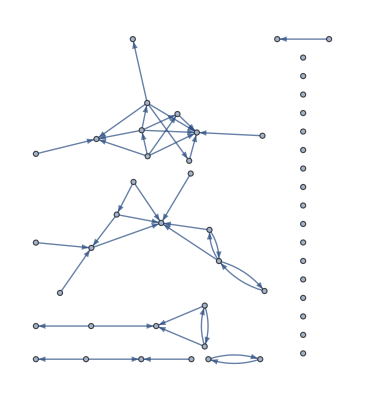

```mathematica
wolframFriendMentionNetwork =twitter["FriendMentionNetwork","Username"-> "WolframResearch"]
```

Identify the network of Twitter users who mention “WolframResearch”:

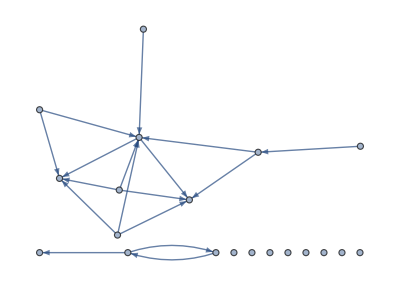

```mathematica
wolframSearchMentionGraph =twitter["SearchMentionNetwork",Query->"WolframResearch"]
```

## Communicate

What is the story your audience is interested in?

How can you recreate the story (reproducible analysis) easily, if:

the data changes

you decide to change one of the methods used for analysis

you decide to include additional analysis in your report

### Setup

Wrangle data for tweets sent out by a specific user for the last 30 days:

```mathematica
username = "WolframResearch";
```

```mathematica
tweetsLastMonth = twitter["TweetList","Username"-> username,MaxItems-> 500,"Elements"-> "FullData"][Select[#Date> DatePlus[-30]&&!StringMatchQ[#Text,StartOfString~~"RT"~~___]&] ,All]
```

```mathematica
tweetsLastMonth = Dataset[getUserMentions /@ Normal@tweetsLastMonth]
```

### Visualisations

WordCloud of hashtags:

```mathematica
hashtagCloud = WordCloud[Normal[tweetsLastMonth[Flatten,"Hashtags"]]]
```

WordCloud of user mentions:

```mathematica
userMentionCloud =WordCloud[Normal[tweetsLastMonth[Flatten,"user_mentions"]]]
```

WordCloud of tweet text excluding hashtags and user mentions:

```mathematica
tweetTextCloud =WordCloud[justWords[ToLowerCase[tweetsLastMonth[StringRiffle[#," "]& ,"Text",cleanText]]]]
```

Most-used hashtags:

```mathematica
rankedHashTags =tweetsLastMonth[Flatten /* Counts /* ReverseSort,"Hashtags"];
top5RankedHashtags = Take[rankedHashTags,5]
```

Hashtags similar to a specific keyword:

```mathematica
focusKeyword = "data";focusKeywordHashtags =Dataset@KeySort@KeySelect[rankedHashTags//Normal,StringMatchQ[#,___~~focusKeyword~~___,IgnoreCase->True]&]
```

Comparison of tweets containing the keyword in focus with all other tweets:

```mathematica
totalTweets =BarChart[{tweetsLastMonth[Select[!StringMatchQ[#Text,___~~focusKeyword~~___,IgnoreCase->True]&]/* Length,"Date"],tweetsLastMonth[Select[StringMatchQ[#Text,___~~focusKeyword~~___,IgnoreCase->True]&]/* Length,"Date"]},ChartLabels->Placed[{"Others",focusKeyword},Above],BarOrigin->Left,
ColorFunction->(ColorData[{"SiennaTones","Reverse"}][#]&),ColorFunctionScaling->True, ChartLayout->"Stacked"]
```

Number of tweets sent on average per day:

```mathematica
perDay =N[Quantity[Length[tweetsLastMonth],"tweets"]/DateDifference@@Normal@tweetsLastMonth[{-1,1} ,"Date"]]
```

Twitter activity by time of day for each day of week:

```mathematica
weeklytweeting =weeklyBuzz[tweetsLastMonth]
```

Comparison of tweets sent out on all topics versus tweets with focus keyword, for the last 30 days:

```mathematica
daycounts =DateHistogram[{tweetsLastMonth[All,"Date"],tweetsLastMonth[Select[StringMatchQ[#Text,___~~focusKeyword~~___,IgnoreCase->True]&],"Date"]},"Day",DateReduction->"Month",LabelingFunction->Tooltip,ChartLayout->"Stacked",ChartLegends->Placed[{"All",focusKeyword},Below],ChartStyle->{RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825]}]
```

Number of tweets liked:

```mathematica
favorited =tweetsLastMonth[Histogram[#,PlotRange-> Full,PlotLabel->"Liked",ColorFunction->(ColorData[{"SiennaTones","Reverse"}][#]&)]&,"FavoriteCount"]
```

Number of tweets that were retweeted:

```mathematica
retweeted =tweetsLastMonth[Histogram[#,PlotRange-> Full,PlotLabel->"Retweeted",ColorFunction->(ColorData[{"SiennaTones","Reverse"}][#]&)]&,"RetweetCount"]
```

Most popular tweets:

```mathematica
highFavoriteCount =Floor[tweetsLastMonth[Max,"FavoriteCount"],5]
```

```mathematica
highRetweetCount =Floor[tweetsLastMonth[Max,"RetweetCount"],5]
```

```mathematica
popular =Reverse@SortBy[Dataset[Normal[tweetsLastMonth[Select[#FavoriteCount > highFavoriteCount||#RetweetCount> highRetweetCount&],{"Text","Hashtags","FavoriteCount","RetweetCount"}]]],{#FavoriteCount&,#RetweetCount&}]
```

Tweets that could have been tagged with “#DataScience”:

```mathematica
predictions =Dataset[<|#["Text"]-> <|"Predicted"-> dsClassifier[#["Text"]],"Hashtags"-> #["Hashtags"]|>&/@ Normal@tweetsLastMonth[All,{"Text","Hashtags"}]|>];
```

```mathematica
revisitTagsFor =predictions[Select[#Predicted == "DataScience" && !MemberQ[ToLowerCase[#Hashtags],ToLowerCase["DataScience"]]&],"Hashtags"]
```

Putting it all together into a compact visualisation:

```mathematica
TabView[
{"Numbers at a Glance"->
Panel[
Grid[
{
{
Column[
{
Row[{Style["Number of tweets per month: ","Subsubsection"],
Style[Length@tweetsLastMonth,18]}],
Row[{Style["Number of tweets per day: ","Subsubsection"],
Style[QuantityMagnitude@perDay,18]}],
Row[{Style["Number of hashtags used: ","Subsubsection"],
Style[Length@rankedHashTags,18]}]
}
],
Show[totalTweets,ImageSize-> Medium]
},
{
Column[
{Style["Top 5 hashtags: ","Subsubsection"],top5RankedHashtags}],
Column[
{Style["Focus hashtags:","Subsubsection"],focusKeywordHashtags}]
}
}
]
],
"Contents of Tweets"->
Panel[
Grid[
{
{Style["Hashtags: ","Subsubsection"],
Style["Tweet Text: ","Subsubsection"]
},
{Show[hashtagCloud,ImageSize-> Medium],
Show[tweetTextCloud,ImageSize-> Medium]
}
}
]
],
"Liked and Retweeted"->
Panel[Grid[{
{Column[{Style["Most popular tweets: ","Subsubsection"],popular}],SpanFromLeft},
{Show[favorited,ImageSize-> Medium],Show[retweeted,ImageSize->Medium]}
}
]
],

"Weekly Buzz"->
Panel[weeklytweeting],
"Daily Numbers"-> 
Panel[
 Show[daycounts,ImageSize-> Medium,PlotLabel-> "Tweets by day of month"]
],
"Revisit Hashtag"->Panel[
Pane[
Column[{Style["Could these tweets possibly have been tagged #"~~focusKeyword~~"? ","Subsubsection"],
Grid[Prepend[List@@@Normal@Normal@revisitTagsFor,Style[#,Bold]&/@ {"Tweet Text","Hashtag"}],Frame-> {False,All},FrameStyle->LightGray,Alignment->Left,BaseStyle->"Text"]}],
{800,500},
Scrollbars->True,
ImageSizeAction->"Scrollable"
]
]},
Alignment->Center]
```

### Report Generation

Using report templates to automatically generate reports containing the information that was manually put together:

```mathematica
NotebookOpen[FileNameJoin[{NotebookDirectory[],"data","TweetAnalysisTemplate.nb"}]]
```

```mathematica
twitter=ServiceConnect["Twitter"];
```

```mathematica
GenerateDocument[FileNameJoin[{NotebookDirectory[],"data","TweetAnalysisTemplate.nb"}],<|"keyword"->"#WolfLang"|>]
```

## Exercise: Reusing the Workflow

Reuse the workflow to perform the same analysis on the Twitter feed of another Twitter account.

Adapt the workflow to analyse the tweets on a particular keyword instead of tweets by a particular user.

## Summary

This section presented the multiparadigm data science workflow to trace the path of a specific project from question to actionable insight.

The workflow is built in stages:

Question

Wrangle

Explore

Analyse

Communicate

The “multiparadigm approach” enhances the workflow:

Options to work with different types of data

Ability to branch out at every stage of the workflow, experiment with cross-disciplinary techniques

Try algorithms driven by the questions—not restricted to traditional methods associated with a certain kind of data or a even a specific field of study

Incorporate data processing, analysis and visualisation capabilities into one start-to-finish workflow

The iterative process enables agile development.

The workflow keeps a well-documented record of your analysis for later reproducibility.

## References

Multiparadigm Data Science with the Wolfram Language

Web Scraping with the Wolfram Language: Part 1 and Part 2 by Brian Wood

Citizen Data Science with Civic Hacking: The Safe Drinking Water Data Challenge by Swede White

Data Science courses on Wolfram U

Data Science discussion group on Wolfram Community

Doing Data Science by Cathy O’Neil and Rachel Schutt

Analyzing Correlations between #BTC Tweets and Bitcoin Trading Using Natural Language Processing by Swede White

## Helper Code

```mathematica
(*DumpSave["WolframTweetsData.mx",{wolframTweets,mentionedUsersData,locations,mentionedUserHashtags,mentionedUserUserMentions,userMentionGraph,userMentionCommunitiesGraph,tweetsLastMonth}];*)
```

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]];
```

```mathematica
weeklyBuzz[tweetsData_] := 
Module[{daysOfWeek = {Monday,Tuesday,Wednesday,Thursday,Friday,Saturday,Sunday},dayOfWeekCounts,max, dailyByHourTweets},
dayOfWeekCounts =Counts[#]& /@GroupBy[{DateObject[#]["DayName"],DateObject[#]["Hour"]}&/@ Normal@tweetsData[All,"Date"],First-> Last];
AssociateTo[dayOfWeekCounts[#],Thread[Complement[Range[1,24],Keys[dayOfWeekCounts[#]]]-> 0]]& /@ Keys@dayOfWeekCounts;
AssociateTo[dayOfWeekCounts, Thread[Complement[daysOfWeek,Keys@dayOfWeekCounts]-> Association@Table[i->0,{i,24}]]];
max =Round[Values[Values[KeySort[#]]& /@ dayOfWeekCounts]//Max,5];
dailyByHourTweets =ArrayPlot[Values@KeySort[dayOfWeekCounts[#]]&/@ daysOfWeek,ColorFunction->(ColorData[{"SiennaTones","Reverse"}][#]&),PlotRange->{0,max},ColorFunctionScaling->True,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{Table[{i,daysOfWeek[[i]]},{i,7}],None},{Range[24],None}},ImageSize->Full,PlotLabel->"WolframResearch Tweets"<>" ("<>DateString[tweetsData[Min,"Date"],{"DateShort"}]<>" to "<>DateString[tweetsData[Max,"Date"],{"DateShort"}]<>")",PlotLegends->Placed[Automatic,Below]]]
```

```mathematica
tweetNonhashtagTextCloud[tweetsDataset_] := WordCloud[StringDelete[Flatten[StringSplit[cleanText /@ Normal[tweetsDataset[All,"Text"]]]],___~~Except[LetterCharacter|DigitCharacter]~~___],
WordSpacings->2]
```

```mathematica
justWords[txt_]:= StringDelete[txt,{"#"|"@"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter}];
```